```mathematica
AppendTo[$Path,NotebookDirectory[]<>"../src"];
<<affine.m;
```

```mathematica
weight[Subscript[B, 2]][1,1]
```

finiteWeight[2,{3/2,1/2}]

```mathematica
tt1=Table[freudenthalMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}];
tt2=Table[racahMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}];
```

```mathematica
Table[freudenthalMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}]
```

{{0.040002,formalElement[Affine`Private`mults$639]},{0.132009,formalElement[Affine`Private`mults$642]},{0.132008,formalElement[Affine`Private`mults$645]},{0.540034,formalElement[Affine`Private`mults$648]},{0.820051,formalElement[Affine`Private`mults$651]},{2.02413,formalElement[Affine`Private`mults$654]},{2.82818,formalElement[Affine`Private`mults$657]},{5.39634,formalElement[Affine`Private`mults$660]},{7.14445,formalElement[Affine`Private`mults$663]},{12.4208,formalElement[Affine`Private`mults$666]}}

```mathematica
Table[racahMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}]
```

{{0.044003,formalElement[Affine`Private`mults$670]},{0.108007,formalElement[Affine`Private`mults$673]},{0.124008,formalElement[Affine`Private`mults$676]},{0.280017,formalElement[Affine`Private`mults$679]},{0.364023,formalElement[Affine`Private`mults$682]},{0.768048,formalElement[Affine`Private`mults$685]},{0.96006,formalElement[Affine`Private`mults$688]},{1.6441,formalElement[Affine`Private`mults$691]},{2.00413,formalElement[Affine`Private`mults$694]},{2.96419,formalElement[Affine`Private`mults$697]}}

```mathematica
Export["timing.pdf",Show[ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt1,{Joined-> True,PlotStyle->Dashed}], ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt2,{Joined-> True,PlotStyle->Thick}]]]
```

timing.pdf

```mathematica
Export["timing.pdf",Out[139]]
```

timing.pdf

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

```mathematica
tt1
```

tt1

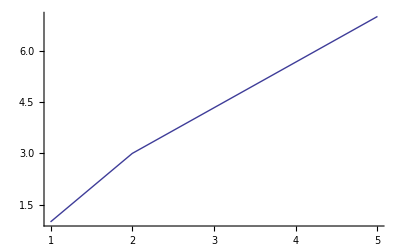

```mathematica
ListPlot[{{1,1},{2,3},{5,7}},Joined->True]
```

```mathematica
Export["timing.pdf",Show[ListPlot[#[[1]]&/@tt1,{Joined->True, PlotStyle->Dashed}],ListPlot[#[[1]]&/@tt2,{Joined-> True,PlotStyle->Thick}]]
```

timing.pdf

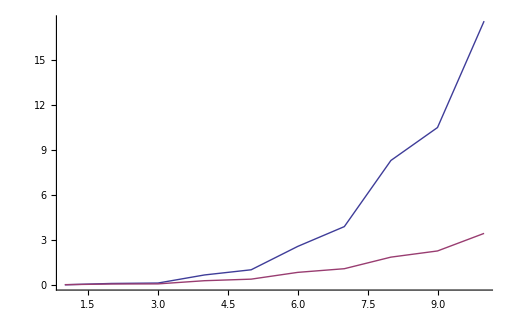

```mathematica
b2=regularSubalgebra[Subscript[B, 4]][3,4]
```

finiteRootSystem[2,4,{finiteWeight[4,{0,0,1,-1}],finiteWeight[4,{0,0,0,1}]}]

```mathematica
brc=simpleBranching[Subscript[B, 4],b2][weight[Subscript[B, 4]][2,2,2,2]]//Timing
```

$Aborted

```mathematica
freudenthalMultiplicities[Subscript[B, 4]][weight[Subscript[B, 4]][2,2,2,2]]//Timing
```

$Aborted

```mathematica
dimension[Subscript[B, 4]][weight[Subscript[B, 4]][2,2,2,2]]
```

43046721

```mathematica
b2=makeSimpleRootSystem[B,2];
vm=makeVermaModule[b2][{2,1},20];
pm=makeParabolicVermaModule[b2][weight[b2][2,1],{1},20];
im=makeIrreducibleModule[b2][2,1];

textPlot[m_module]:=drawPlaneProjection[2,1,character[m],{Frame->True,GridLines->Automatic,PlotRange->{{-3,3},{-3,3}}, PlotRangeClipping->True}];
```

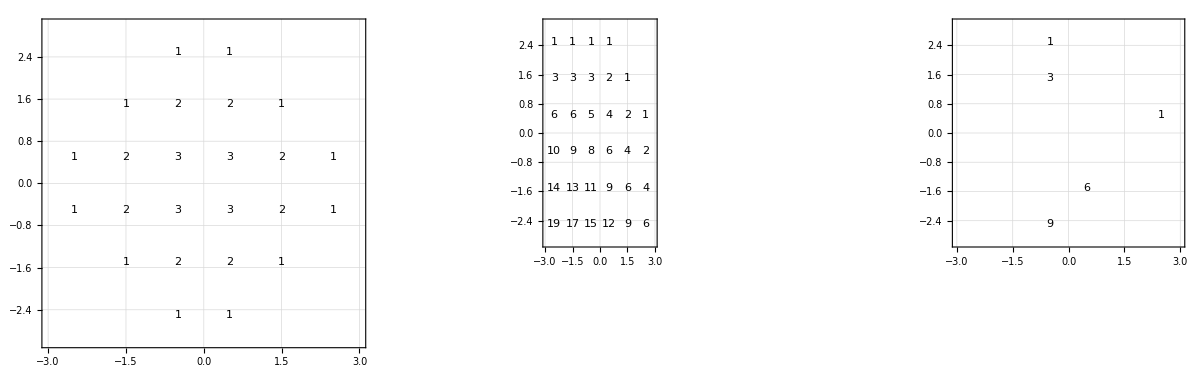

```mathematica
GraphicsRow[textPlot/@{im,vm,pm}]
```

```mathematica
Export["irrep-verma-pverma.pdf",GraphicsRow[textPlot/@{im,vm,pm}]]
```

irrep-verma-pverma.pdf

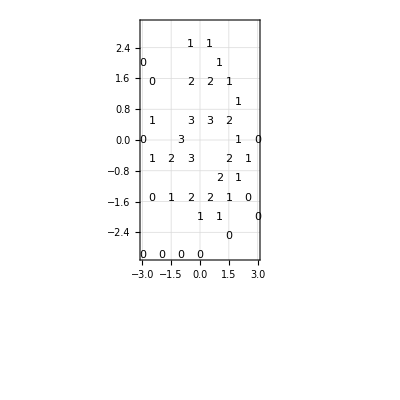

```mathematica
im1=makeIrreducibleModule[Subscript[B, 2]][2,1];
im2=makeIrreducibleModule[Subscript[B, 2]][1,2];
textPlot[im1 ⊕ im2]
```

```mathematica
Export["irrep-sum.pdf",textPlot[im1 ⊕ im2]]
```

irrep-sum.pdf

```mathematica
?CirclePlus
```

CirclePlus[x,y,…] displays as x⊕y⊕….
 Direct sum of finite-dimensional and affine Lie algebras can be specified as sum of root systems
 denotes direct sum of modules

```mathematica
draw3dProjection[1,2,3,character[makeIrreducibleModule[Subscript[A, 1]][3]⊗makeIrreducibleModule[Subscript[B, 2]][3,1]],{FaceGrids->All,Axes->True}]
```

-Graphics3D-

```mathematica
weight[Subscript[G, 2]][1,1]
```

finiteWeight[3,{-1,-2,3}]

```mathematica
?GridLines
```

GridLines is an option for two-dimensional graphics functions that specifies grid lines.

```mathematica
simpleBranching[Subscript[B, 4],parabolicSubalgebra[Subscript[B, 4]][2,3,4]][weight[Subscript[B, 4]][1,2,0,0]]//Timing
```

{13.7569,formalElement[Affine`Private`table$15934]}

```mathematica
Out[145][weights]
```

{finiteWeight[4,{0,2,1,0}],finiteWeight[4,{0,2,0,0}],finiteWeight[4,{0,1,1,1}],finiteWeight[4,{0,1,1,0}],finiteWeight[4,{0,1,0,0}],finiteWeight[4,{0,0,0,0}]}

```mathematica
Out[145][multiplicities]
```

{1,2,0,2,4,2}

```mathematica
ourBranching[Subscript[B, 4],parabolicSubalgebra[Subscript[B, 4]][2,3,4]][weight[Subscript[B, 4]][1,1,0,0]]//Timing
```

{4.7403,formalElement[Affine`Private`table$14610]}

```mathematica
Out[149][weights]
```

{finiteWeight[4,{0,3,2,1}],finiteWeight[4,{0,3,2,0}],finiteWeight[4,{0,3,1,1}],finiteWeight[4,{0,3,1,0}],finiteWeight[4,{0,2,2,2}],finiteWeight[4,{0,2,2,1}],finiteWeight[4,{0,2,2,0}],finiteWeight[4,{0,3,0,0}],finiteWeight[4,{0,2,1,1}],finiteWeight[4,{0,2,1,0}],finiteWeight[4,{0,2,0,0}],finiteWeight[4,{0,1,1,1}],finiteWeight[4,{0,1,1,0}],finiteWeight[4,{0,1,0,0}],finiteWeight[4,{0,0,0,0}]}

```mathematica
Out[149][multiplicities]
```

{0,0,0,0,0,0,0,0,0,1,2,0,2,4,2}

```mathematica
ourBranching[makeIrreducibleModule[Subscript[B, 4]][1,2,0,0],parabolicSubalgebra[Subscript[B, 4]][2,3,4]]//Timing
```

{3.78024,formalElement[Affine`Private`table$15926]}

```mathematica
Out[154][[2]][weights]
```

{finiteWeight[4,{0,2,1,1}],finiteWeight[4,{0,2,1,0}],finiteWeight[4,{0,2,0,0}],finiteWeight[4,{0,1,1,1}],finiteWeight[4,{0,1,1,0}],finiteWeight[4,{0,1,0,0}],finiteWeight[4,{0,0,0,0}]}

```mathematica
Out[154][[2]][multiplicities]
```

{0,1,2,0,2,4,2}

```mathematica
tt3=Timing[simpleBranching[Subscript[B, 4],parabolicSubalgebra[Subscript[B, 4]][2,3,4]][weight[Subscript[B, 4]][Sequence@@#]]]&/@ Flatten[IntegerPartitions[#,{4},Range[0,#]]&/@Range[3],1]
```

{{0.380024,formalElement[Affine`Private`table$1278]},{1.06807,formalElement[Affine`Private`table$1299]},{2.35215,formalElement[Affine`Private`table$1334]},{2.80418,formalElement[Affine`Private`table$1383]},{7.25245,formalElement[Affine`Private`table$1439]},{42.6307,formalElement[Affine`Private`table$1516]}}

```mathematica
Flatten[IntegerPartitions[#,{4},Range[0,#]]&/@Range[3],1]
```

{{1,0,0,0},{2,0,0,0},{1,1,0,0},{3,0,0,0},{2,1,0,0},{1,1,1,0}}

```mathematica
Table[{i,i,0,0},{i,0,5}]
```

{{0,0,0,0},{1,1,0,0},{2,2,0,0},{3,3,0,0},{4,4,0,0},{5,5,0,0}}

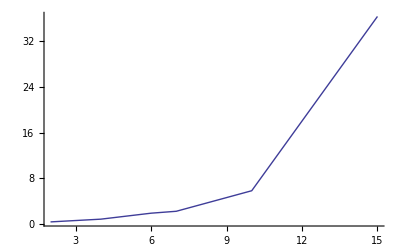

```mathematica
ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt3,{Joined->True}]
```

```mathematica
simpleBranching[Subscript[B, 4],parabolicSubalgebra[Subscript[B, 4]][2,3,4]][weight[Subscript[B, 4]][1,2,0,0]]//Timing
```

```mathematica
tt4=Timing[ourBranching[makeIrreducibleModule[Subscript[B, 4]][Sequence@@#],parabolicSubalgebra[Subscript[B, 4]][2,3,4]]]&/@ 
Table[{i,i,0,0},{i,0,5}]
```

{{4.08825,formalElement[Affine`Private`table$2053]},{3.91625,formalElement[Affine`Private`table$2601]},{4.7403,formalElement[Affine`Private`table$3362]},{5.34834,formalElement[Affine`Private`table$4397]},{6.80843,formalElement[Affine`Private`table$5816]},{7.88049,formalElement[Affine`Private`table$7694]}}

```mathematica
TableFlatten[Permutations[Flatten[IntegerPartitions[#,{4},Range[0,#]]&/@Range[3],1]],1]
```

$Aborted

```mathematica
Flatten[Table[{i,j,0,0},{i,0,3},{j,0,i}],1]
```

{{0,0,0,0},{1,0,0,0},{1,1,0,0},{2,0,0,0},{2,1,0,0},{2,2,0,0},{3,0,0,0},{3,1,0,0},{3,2,0,0},{3,3,0,0}}

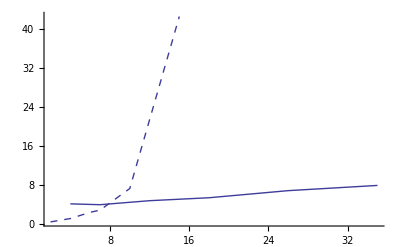

```mathematica
Show[ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt3,{Joined->True, PlotStyle->Dashed}],
ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt4,{Joined->True, PlotStyle->Thick}]]
```

```mathematica
Export["branching-timing.pdf",Out[18]]
```

branching-timing.pdf

```mathematica
fm=makeIrreducibleModule[b2][1,0]
```

module[finiteRootSystem[2,2,{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}],formalElement[Affine`Private`table$202847],finiteRootSystem[2,2,{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}],10]

```mathematica
tp=((fm⊗fm)⊗fm)⊗fm
```

module[finiteRootSystem[8,8,{finiteWeight[8,{1,-1,0,0,0,0,0,0}],finiteWeight[8,{0,1,0,0,0,0,0,0}],finiteWeight[8,{0,0,1,-1,0,0,0,0}],finiteWeight[8,{0,0,0,1,0,0,0,0}],finiteWeight[8,{0,0,0,0,1,-1,0,0}],finiteWeight[8,{0,0,0,0,0,1,0,0}],finiteWeight[8,{0,0,0,0,0,0,1,-1}],finiteWeight[8,{0,0,0,0,0,0,0,1}]}],formalElement[Affine`Private`table$203158],finiteRootSystem[8,8,{finiteWeight[8,{1,-1,0,0,0,0,0,0}],finiteWeight[8,{0,1,0,0,0,0,0,0}],finiteWeight[8,{0,0,1,-1,0,0,0,0}],finiteWeight[8,{0,0,0,1,0,0,0,0}],finiteWeight[8,{0,0,0,0,1,-1,0,0}],finiteWeight[8,{0,0,0,0,0,1,0,0}],finiteWeight[8,{0,0,0,0,0,0,1,-1}],finiteWeight[8,{0,0,0,0,0,0,0,1}]}],10000]

```mathematica
Affine`Private`rootSystem[tp]
```

finiteRootSystem[8,8,{finiteWeight[8,{1,-1,0,0,0,0,0,0}],finiteWeight[8,{0,1,0,0,0,0,0,0}],finiteWeight[8,{0,0,1,-1,0,0,0,0}],finiteWeight[8,{0,0,0,1,0,0,0,0}],finiteWeight[8,{0,0,0,0,1,-1,0,0}],finiteWeight[8,{0,0,0,0,0,1,0,0}],finiteWeight[8,{0,0,0,0,0,0,1,-1}],finiteWeight[8,{0,0,0,0,0,0,0,1}]}]

```mathematica
subs=makeFiniteRootSystem[{1/2*{1,-1,1,-1},1/2*{0,1,0,1}}]
```

finiteRootSystem[2,4,{finiteWeight[4,{1/2,-1/2,1/2,-1/2}],finiteWeight[4,{0,1/2,0,1/2}]}]

```mathematica
subs=makeFiniteRootSystem[{1/4*{1,-1,1,-1,1,-1,1,-1},1/4*{0,1,0,1,0,1,0,1}}]
```

finiteRootSystem[2,8,{finiteWeight[8,{1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4,-1/4}],finiteWeight[8,{0,1/4,0,1/4,0,1/4,0,1/4}]}]

```mathematica
bc=ourBranching[tp,subs]
```

formalElement[Affine`Private`table$204101]

```mathematica
CirclePlus [{bc[#], dynkinLabels[subs][#]}&/@bc[weights]]
```

CirclePlus[{{1,{4,0}},{3,{2,2}},{0,{3,0}},{2,{0,4}},{3,{1,2}},{6,{2,0}},{6,{0,2}},{1,{1,0}},{3,{0,0}}}]

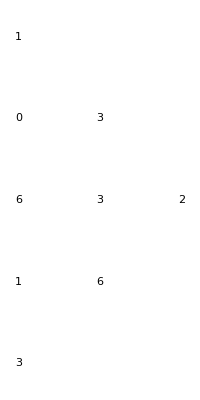

```mathematica
drawPlaneProjection[2,1,bc]
```

```mathematica
tp2=fm⊗fm
```

module[finiteRootSystem[4,4,{finiteWeight[4,{1,-1,0,0}],finiteWeight[4,{0,1,0,0}],finiteWeight[4,{0,0,1,-1}],finiteWeight[4,{0,0,0,1}]}],formalElement[Affine`Private`table$204115],finiteRootSystem[4,4,{finiteWeight[4,{1,-1,0,0}],finiteWeight[4,{0,1,0,0}],finiteWeight[4,{0,0,1,-1}],finiteWeight[4,{0,0,0,1}]}],100]

```mathematica
subs2=makeFiniteRootSystem[{1/2*{1,-1,1,-1},1/2*{0,1,0,1}}]
```

finiteRootSystem[2,4,{finiteWeight[4,{1/2,-1/2,1/2,-1/2}],finiteWeight[4,{0,1/2,0,1/2}]}]

```mathematica
bc2=ourBranching[tp2,subs2]
```

formalElement[Affine`Private`table$204262]

```mathematica
bc2[weights]
```

{finiteWeight[4,{1,0,1,0}],finiteWeight[4,{1/2,1/2,1/2,1/2}],finiteWeight[4,{1/2,0,1/2,0}],finiteWeight[4,{0,0,0,0}]}

```mathematica
bc2[multiplicities]
```

{1,1,0,1}

```mathematica
dimension[b2][weight[b2][1,0]]
```

5

```mathematica
5^4
```

625

```mathematica
Plus@@((dimension[subs]/@bc[weights]).bc[multiplicities])
```

625

```mathematica
dimension[subs]/@bc[weights]
```

{55,81,30,35,35,14,10,5,1}

```mathematica
stringFunctions[OverHat[Subscript[A, 2]],{1,1,2}]
```

{{{0,0,4},2 q+10 q^2+40 q^3+133 q^4+398 q^5+1084 q^6+2760 q^7+6632 q^8+15214 q^9+33508 q^10},{{0,3,1},2 q+12 q^2+49 q^3+166 q^4+494 q^5+1340 q^6+3387 q^7+8086 q^8+18415 q^9+40302 q^10},{{1,1,2},1+6 q+27 q^2+96 q^3+298 q^4+836 q^5+2173 q^6+5310 q^7+12341 q^8+27486 q^9+59029 q^10},{{2,2,0},1+8 q+35 q^2+124 q^3+379 q^4+1052 q^5+2700 q^6+6536 q^7+15047 q^8+33248 q^9+70877 q^10},{{3,0,1},2+12 q+49 q^2+166 q^3+494 q^4+1340 q^5+3387 q^6+8086 q^7+18415 q^8+40302 q^9+85226 q^10}}

```mathematica
branchingFunctions[OverHat[Subscript[B, 2]],makeAffineExtension[makeFiniteRootSystem[{{1,1}}]],{1,1,1}]
```

{{{3,0},2+14 q+52 q^2+154 q^3+410 q^4+994 q^5+2248 q^6+4832 q^7+9934 q^8+19680 q^9+37802 q^10},{{2,1},4+20 q+72 q^2+220 q^3+584 q^4+1424 q^5+3248 q^6+7012 q^7+14488 q^8+28844 q^9+55616 q^10},{{0,3},4 q+20 q^2+68 q^3+200 q^4+516 q^5+1224 q^6+2736 q^7+5808 q^8+11820 q^9+23236 q^10},{{1,2},2+14 q+54 q^2+168 q^3+462 q^4+1148 q^5+2656 q^6+5812 q^7+12130 q^8+24358 q^9+47328 q^10}}

```mathematica
Out[263]//MatrixForm
```

({3,0} | 2+14 q+52 q^2+154 q^3+410 q^4+994 q^5+2248 q^6+4832 q^7+9934 q^8+19680 q^9+37802 q^10
{2,1} | 4+20 q+72 q^2+220 q^3+584 q^4+1424 q^5+3248 q^6+7012 q^7+14488 q^8+28844 q^9+55616 q^10
{0,3} | 4 q+20 q^2+68 q^3+200 q^4+516 q^5+1224 q^6+2736 q^7+5808 q^8+11820 q^9+23236 q^10
{1,2} | 2+14 q+54 q^2+168 q^3+462 q^4+1148 q^5+2656 q^6+5812 q^7+12130 q^8+24358 q^9+47328 q^10)

```mathematica
α=simpleRoots[Subscript[G, 2]]
```

{finiteWeight[3,{1,-1,0}],finiteWeight[3,{-2,1,1}]}

```mathematica
ort={α[[1]],α[[2]]-1/2*α[[1]]*(α[[2]].α[[1]])}
```

{finiteWeight[3,{1,-1,0}],finiteWeight[3,{-1/2,-1/2,1}]}

```mathematica
ort=(1/(#.#)^(1/2))*#&/@ort
```

{finiteWeight[3,{1/(√2),-1/(√2),0}],finiteWeight[3,{-1/(√6),-1/(√6),√(2/3)}]}

```mathematica
ch=character[makeParabolicVermaModule[Subscript[G, 2]][weight[Subscript[G, 2]][1,1],{2}]]
```

formalElement[Affine`Private`table$11006]

```mathematica
ch=character[makeVermaModule[Subscript[G, 2]][{1,1}]]
```

formalElement[Affine`Private`table$10919]

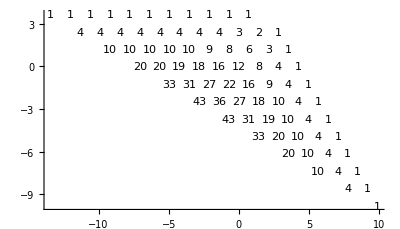

```mathematica
Graphics[Text[ch[#],{#.ort[[1]],#.ort[[2]]}]&/@ch[weights],{Axes->True}]
```

```mathematica
ch=character[makeIrreducibleModule[Subscript[G, 2]][weight[Subscript[G, 2]][1,1]]]
```

formalElement[Affine`Private`table$11104]

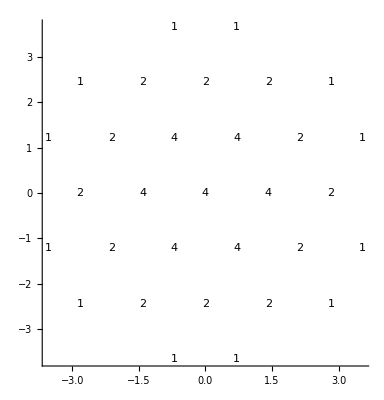

```mathematica
Graphics[Text[ch[#],{#.ort[[1]],#.ort[[2]]}]&/@ch[weights],{Axes->True}]
```

```mathematica
ch1=formalOrbit[Subscript[G, 2]][weight[Subscript[G, 2]][1,1]+rho[Subscript[G, 2]]]
```

formalElement[Affine`Private`table$11139]

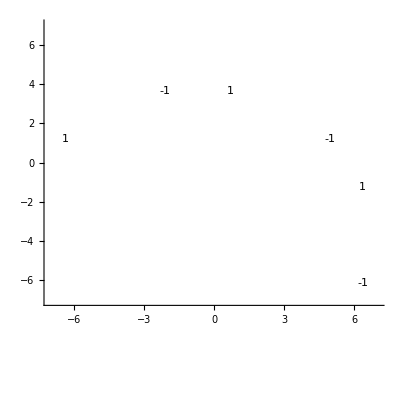

```mathematica
Graphics[Text[ch1[#],{(#-rho[Subscript[G, 2]]).ort[[1]],(#-rho[Subscript[G, 2]]).ort[[2]]}]&/@ch1[weights],{Axes->True,PlotRange->{{-7,7},{-7,7}}}]
```

```mathematica
gr[ch1_]:=Graphics[Text[If[ch1[#]<100,ch1[#],".."],{#.ort[[1]],#.ort[[2]]}]&/@ch1[weights],{Frame->True,GridLines->{{-8,-4,0,4},{-8,-4,0,4}},GridLinesStyle->Directive[Gray,Dashed],PlotRangeClipping->True,PlotRange->{{-9,5},{-10,5}}}]
```

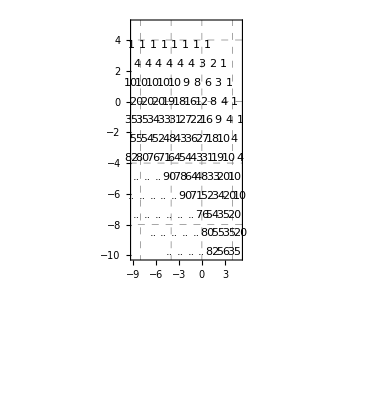
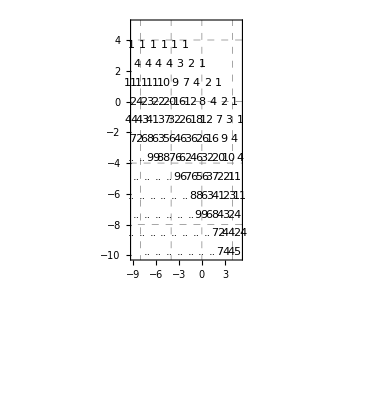
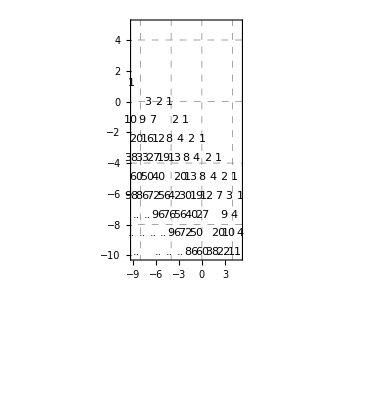
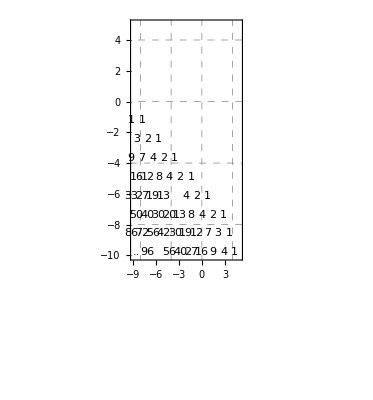
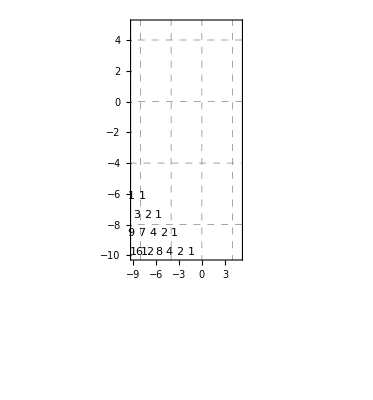
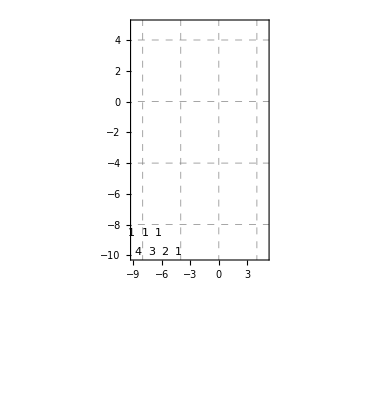

```mathematica
graphs=gr[character[makeParabolicVermaModule[Subscript[G, 2]][#-rho[Subscript[G, 2]],{2},20]]]&/@Select[ch1[weights],#.α[[2]]≥0&]
```

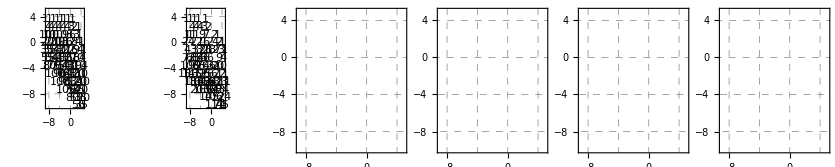

```mathematica
GraphicsRow[Out[129]]
```

```mathematica
Select[ch1[weights],#.α[[2]]≥0&]
```

{finiteWeight[3,{-2,-4,6}],finiteWeight[3,{-4,-2,6}],finiteWeight[3,{-6,2,4}],finiteWeight[3,{-6,4,2}],finiteWeight[3,{-4,6,-2}],finiteWeight[3,{-2,6,-4}]}

```mathematica
ch1/@Out[138]
```

{1,-1,1,-1,1,-1}

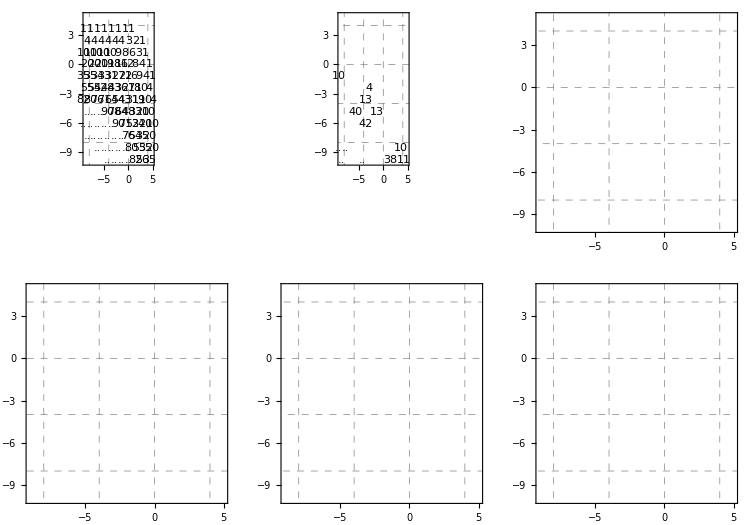

```mathematica
GraphicsGrid[{graphs[[{1,3,5}]],graphs[[{2,4,6}]]}]
```

```mathematica
Export["G2-pverma.pdf",GraphicsGrid[{graphs[[{1,3,5}]],graphs[[{2,4,6}]]}]]
```

G2-pverma.pdf

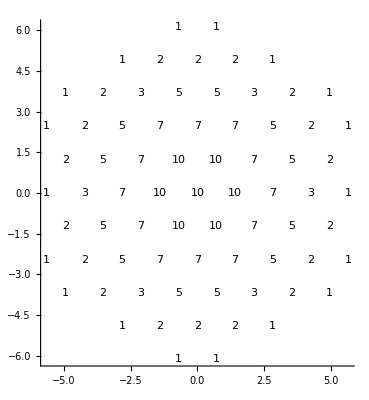

```mathematica
gr[ch]
```

```mathematica
OverHat[Subscript[C, 3]][gradeLimit]=7
```

7

```mathematica
OverHat[parabolicSubalgebra[Subscript[B, 3]][2,3]][gradeLimit]=
```

5

```mathematica
OverHat[parabolicSubalgebra[Subscript[C, 3]][2,3]][gradeLimit]=7
```

7

```mathematica
branchingFunctions[OverHat[Subscript[C, 3]],OverHat[parabolicSubalgebra[Subscript[C, 3]][2,3]],{2,0,0,0}]
```

{{{0,1,0},2 q-20 q^3+24 q^4+82 q^5-320 q^6+108 q^7},{{1,0,0},1-q-8 q^2+19 q^3+16 q^4-156 q^5+205 q^6+640 q^7},{{0,0,1},q-5 q^3+7 q^5}}

```mathematica
prs=OverHat[parabolicSubalgebra[Subscript[C, 3]][2,3]]
```

affineRootSystem[2,finiteRootSystem[2,3,{finiteWeight[3,{0,1,-1}],finiteWeight[3,{0,0,2}]}],affineWeight[3,finiteWeight[3,{0,-2,0}],0,1],{affineWeight[3,finiteWeight[3,{0,1,-1}],0,0],affineWeight[3,finiteWeight[3,{0,0,2}],0,0]}]

```mathematica
weight[prs][0,0,1]
```

affineWeight[3,finiteWeight[3,{0,1,1}],1,0]

```mathematica
weight[prs][1,0,0]
```

affineWeight[3,finiteWeight[3,{0,0,0}],1,0]

```mathematica
bbc=branching[makeIrreducibleModule[Subscript[C, 3]][1,0,0],parabolicSubalgebra[Subscript[C, 3]][2,3]]
```

formalElement[Affine`Private`table$62145]

```mathematica
dynkinLabels[parabolicSubalgebra[Subscript[C, 3]][2,3]]/@bbc[weights]
```

{{0,1},{1,0},{0,0}}

```mathematica
Out[106]
```

```mathematica
branchingFunctions[OverHat[Subscript[B, 3]],OverHat[parabolicSubalgebra[Subscript[B, 3]][2,3]],{1,1,0,0}]
```

{{{0,2,0},2 q+4 q^2+12 q^3+24 q^4+50 q^5},{{1,1,0},1+5 q+13 q^2+29 q^3+64 q^4+126 q^5},{{2,0,0},2+4 q+12 q^2+24 q^3+50 q^4+92 q^5},{{0,0,2},2 q+5 q^2+18 q^3+37 q^4+83 q^5}}

```mathematica
OverHat[Subscript[D, 4]][gradeLimit]=6
```

6

```mathematica
OverHat[parabolicSubalgebra[Subscript[D, 4]][1,2,3]][gradeLimit]=6
```

6

```mathematica
branchingFunctions[OverHat[Subscript[D, 4]],OverHat[parabolicSubalgebra[Subscript[D, 4]][1,2,3]],{1,2,1,2,0}]
```

$Aborted

```mathematica
parabolicSubalgebra[Subscript[D, 4]][1,2,3]
```

finiteRootSystem[3,4,{finiteWeight[4,{1,-1,0,0}],finiteWeight[4,{0,1,-1,0}],finiteWeight[4,{0,0,1,-1}]}]

```mathematica
Subscript[A, 3]
```

finiteRootSystem[3,4,{finiteWeight[4,{1,-1,0,0}],finiteWeight[4,{0,1,-1,0}],finiteWeight[4,{0,0,1,-1}]}]

```mathematica
brrr=branching[makeIrreducibleModule[Subscript[D, 4]][2,1,2,0],Subscript[A, 3]]
```

formalElement[Affine`Private`table$42074]

```mathematica
Out[102][multiplicities]
```

{0,0,1,0,2,0,2,1,2,1,1,0,0,0}

```mathematica
dynkinLabels[Subscript[A, 3]][projection[Subscript[A, 3]][weight[Subscript[D, 4]][1,1,1,0]]]
```

{1,1,1}

```mathematica
dynkinLabels[Subscript[A, 3]]/@Out[78][weights]
```

{{3,1,1},{2,1,2},{1,2,1},{2,0,2},{0,3,0},{1,1,1},{0,2,0},{1,0,1},{0,1,0},{0,0,0}}

```mathematica
fe=projection[Subscript[A, 3]][Affine`Private`cSingularWeights[makeIrreducibleModule[Subscript[D, 4]][1,1,1,0]]]
```

formalElement[Affine`Private`table$37970]

```mathematica
dynkinLabels[Subscript[A, 3]]/@fe[weights]
```

{{1,1,1}}

```mathematica
fe[multiplicities]
```

{1}

```mathematica
fan[Subscript[D, 4],Subscript[A, 3]]
```

formalElement[Affine`Private`table$38050]

```mathematica
dynkinLabels[Subscript[A, 3]]/@Out[91][weights]
```

{{-2,1,0},{2,0,0},{0,1,0},{2,-1,0},{0,1,-2},{1,-2,1},{-1,0,-1},{0,-1,0},{1,-1,-1},{1,0,1},{1,-1,1},{-1,0,1},{1,0,-1},{0,0,2},{-2,0,0},{-1,2,-1},{-1,-1,1},{-1,1,1},{0,2,-2},{0,-1,2},{0,0,0},{-1,1,-1},{2,-2,0},{1,1,-1},{0,0,-2},{0,-2,2},{-2,2,0}}

```mathematica
Out[91][multiplicities]
```

{2,-1,-4,2,2,2,2,-4,2,2,-4,-4,-4,-1,-1,2,2,2,-1,2,8,-4,-1,2,-1,-1,-1}

```mathematica
OverHat[parabolicSubalgebra[Subscript[C, 3]][2,3]]
```

affineRootSystem[2,finiteRootSystem[2,3,{finiteWeight[3,{0,1,-1}],finiteWeight[3,{0,0,2}]}],affineWeight[3,finiteWeight[3,{0,-2,0}],0,1],{affineWeight[3,finiteWeight[3,{0,1,-1}],0,0],affineWeight[3,finiteWeight[3,{0,0,2}],0,0]}]

```mathematica
parabolicSubalgebra[Subscript[C, 3]][2,3]
```

finiteRootSystem[2,3,{finiteWeight[3,{0,1,-1}],finiteWeight[3,{0,0,2}]}]

```mathematica
Affine`Private`
```

```mathematica
?Symbol*
```

RowBox[{"Symbol", "[", StyleBox["\"\!\(\*StyleBox[\"name\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] refers to a symbol with the specified name.

```mathematica
?#&/@Names["Affine`*"]
```

Information::nomatch: No symbol matching "#&/@Names[\"Affine`*\"]" found.

```mathematica
??
```

Information::basic: ?Name gives information on Name, ?Ab* on all symbols starting with Ab. ??Name gives more information.

```mathematica
Information/@Names["Affine`*"]
```

```mathematica
1
```

$Aborted

```mathematica
?Arrow
```

Arrow[{pt_1,pt_2}] is a graphics primitive which represents an arrow from pt_1 to pt_2.
Arrow[{pt_1,pt_2},s] represents an arrow with its ends set back from pt_1 and pt_2 by a distance s. 
Arrow[{pt_1,pt_2},{s_1,s_2}] sets back by s_1 from pt_1 and s_2 from pt_2. 
Arrow[curve,…] represents an arrow following the specified curve.

```mathematica
pr=Union[positiveRoots[Subscript[G, 2]],-positiveRoots[Subscript[G, 2]]];
```

```mathematica
?Gray
```

Gray represents the color gray in graphics or style specifications.

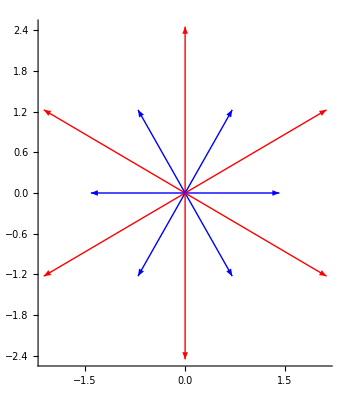

```mathematica
Graphics[{If[#.#==2,Blue,Red],Arrow[{{0,0},{#.ort[[1]],#.ort[[2]]}}]}&/@pr,{Axes->True}]
```

```mathematica
se=singularElement[makeIrreducibleModule[Subscript[G, 2]][1,0]]
```

formalElement[Affine`Private`table$97380]

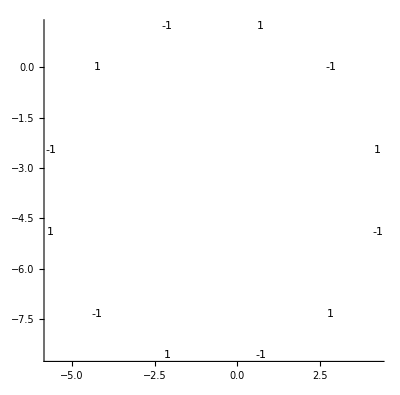

```mathematica
Graphics[Text[se[#],{#.ort[[1]],#.ort[[2]]}]&/@se[weights],{Axes->True}]
```

```mathematica
#.#&/@positiveRoots[Subscript[G, 2]]
```

{2,6,6,2,2,6}

```mathematica
sr=Select[positiveRoots[Subscript[G, 2]],#.#==2&]
```

{finiteWeight[3,{1,-1,0}],finiteWeight[3,{-1,0,1}],finiteWeight[3,{0,-1,1}]}

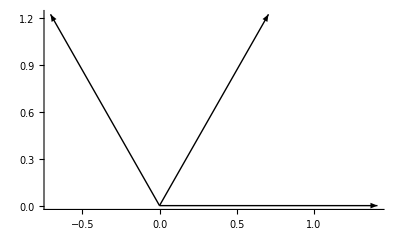

```mathematica
Graphics[Arrow[{{0,0},{#.ort[[1]],#.ort[[2]]}}]&/@sr,{Axes->True}]
```

```mathematica
subs=makeFiniteRootSystem[{sr[[1]],sr[[3]]}]
```

finiteRootSystem[2,3,{finiteWeight[3,{1,-1,0}],finiteWeight[3,{0,-1,1}]}]

```mathematica
cartanMatrix[subs]
```

{{2,1},{1,2}}

```mathematica
dynkinLabels[Subscript[A, 2]][weight[Subscript[G, 2]][0,-1]]
```

{0,3}

```mathematica
brc=simpleBranching[Subscript[G, 2],Subscript[A, 2]][weight[Subscript[G, 2]][0,1]]
```

formalElement[Affine`Private`table$99627]

```mathematica
brc=character[makeIrreducibleModule[Subscript[G, 2]][1,1]]
```

formalElement[Affine`Private`table$99330]

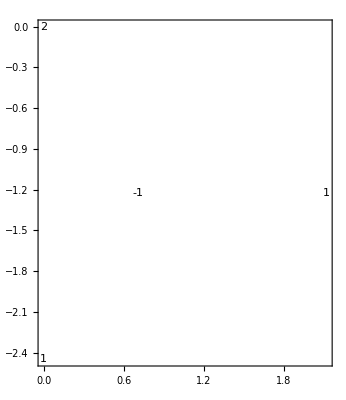

```mathematica
Graphics[Text[brc[#],{#.ort[[1]],#.ort[[2]]}]&/@brc[weights],{Frame->True}]
```

```mathematica
fn=fan[Subscript[G, 2],subs]
```

formalElement[Affine`Private`table$99414]

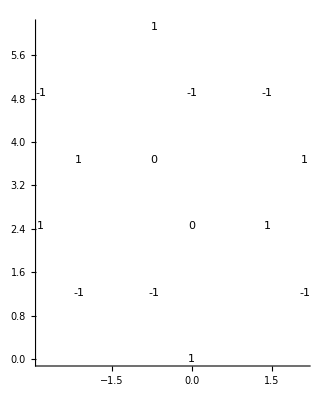

```mathematica
Graphics[Text[fn[#],{#.ort[[1]],#.ort[[2]]}]&/@fn[weights],{Axes->True}]
```